Tavis-Cummings hamiltonian Mathematica notebook. Hey look, it auto-slanties the letters in Mathematica! Well that’s just crazy. Anyways, using the following Hamiltonian
H_TC/ℏω=a^†a  + 1/2(σ_z^(1) + σ_z^(2)) + G(x)((a((σ_+)^(1)+ (σ_+)^(2)) + a^†((σ_-)^(1)+ (σ_-)^(2))))
where the σ stuff is the standard σ stuff, the (n) superscripts are for each atom, and G(x) is the scaled positionally dependant atom-field coupling term. note that the ω terms between the number operator and the atom from the σ_z  are the same for each atom, so that is why it was chosen to divide out. Convenience and stuff. 
The plan here is to construct that hamiltonian with the following states e,e,n-2,e,g,n-1,g,e,n-1,g,g,n where n is the number of photons, g is the ground state of the atom and e is the excited state of the two level atom.

```mathematica
HTC[n_,G1_,G2_] = {{n-1,G1*√(n-1),G2*√(n-1),0},
			{G1*√(n-1),n-1,0,G1*√n},
			{G2*√(n-1),0,n-1,G2*√n},
			{0,G1*√n,G2*√n,n-1}};
```

```mathematica
HTC[n,G1,G2]//MatrixForm
```

(-1+n | G1 √(-1+n) | G2 √(-1+n) | 0
G1 √(-1+n) | -1+n | 0 | G1 √n
G2 √(-1+n) | 0 | -1+n | G2 √n
0 | G1 √n | G2 √n | -1+n)

Well, to begin, let’s just solve the case where the function G is at constant associated with the atom-field coupling. Here, as it’s a ratio of the atomic-transition frequency ω, we weill set it to one as that will be the ideal zero-detuning case. I like the number 10, so that’s how many photons that will be considered here. First, the eigen vectors

```mathematica
$Assumptions -> n>0
```

True→n>0

```mathematica
State = {};
Do[
AppendTo[State,
Normalize[
Eigenvectors[
HTC[1,1]
][[i]]]

], {i,1,4}
];Orthogonalize[State] ;(*Make sure vectors are orthogonal*)
```

Then define a function that exponentiates (spelling?) the time evolution of the Hamiltonian. But first, define ϵ = ℏω then define a time unit such that τ = 2π/ω = 2πℏ/ϵ = 2π ⇒ t = τt’ where t’ is a scaled time unit

```mathematica
TimeEvolution[Eval_,Evec_]:= (*Function constructs exponential matrix for time evolution*)

(T = 0;
Do[T = FullSimplify[
T + Exp[-I*t*2π*Eval[[i]]]*
Outer[Times,Evec[[i]],Evec[[i]]]
],
{i,1,Length[Eval]}];T)
```

```mathematica
Time = TimeEvolution[Ev,State]
```

{{1,0,0,0},{0,Cos[√2 π t]^2,-Sin[√2 π t]^2,-(ⅈ Sin[2 √2 π t])/(√2)},{0,-Sin[√2 π t]^2,Cos[√2 π t]^2,-(ⅈ Sin[2 √2 π t])/(√2)},{0,-(ⅈ Sin[2 √2 π t])/(√2),-(ⅈ Sin[2 √2 π t])/(√2),Cos[2 √2 π t]}}

Now, let’s say we were initially in the state e,e,n-2 =(1
0
0
0) we would then have in our previous notation

```mathematica
P =FullSimplify[Time.{0,1,0,0}];
P//MatrixForm
```

Where we then see that the probability amplitudes for each state are then given by the magnitude of each component that vector in oru state basis. If we were to plot these we would then have

```mathematica
$Assumptions -> t ∈ Reals
```

True→t∈Reals

```mathematica
ColourScheme = {Red,Purple,Green,Blue};
```

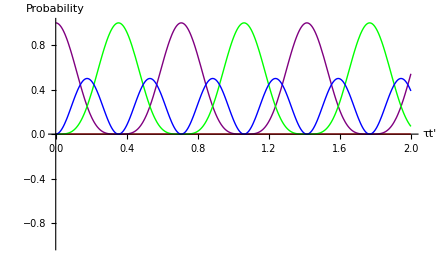

```mathematica
Show[Table[Plot[P[[i]]*Conjugate[P[[i]]],{t,0,2},PlotStyle -> ColourScheme[[i]]],{i,1,4}]
,AxesLabel -> {"τt'","Probability"}]
```

Where i think this makes sense. Where the probablility of the mixed states are maximum, there’s also an equal probability that both are excited or both are in the ground state. ANd now, when something is 100% probable, everything else is zero

Below is a function that does all of the above, just you can change parameters of the Hamiltonian much easier and it outputs a plot.

```mathematica
Needs["PlotLegends`"];
```

```mathematica
SuperFunction[Ham_,IV_,x1_,x2_]:= 
Module[
{States,ev,T,P,t,plot},
Needs["PlotLegends`"];
States = {};
T = 0;
ev = 0;
Do[
AppendTo[States,
Normalize[Eigenvectors[Ham][[j]]]],
{j,1,Length[Ham]}
];
Orthogonalize[States];
ev = Eigenvalues[Ham];   (*Solve the Hamiltonian and hey orthogonal eigenvectors*)
Do[T = FullSimplify[
T + Exp[-I*t*2π*ev[[i]]]*
Outer[Times,States[[i]],States[[i]]]  (*Evolve the system in time by exponentiating the hamiltonian*)
],
{i,1,Length[ev]}];
P = T.IV;
$Assumptions -> t ∈ Reals;
plot= Plot[Evaluate@Table[P[[i]]*Conjugate[P[[i]]],{i,1,Length[ev]}],{t,x1,x2},Frame->True,FrameLabel -> {"Scaled Time","Probability"},PlotLegend -> {"e,e,n-2","e,g,n-1","g,e,n-1","g,g,n"},LegendPosition -> {1,-.25},LegendShadow -> None,LegendBorder -> False,PlotRangePadding->None,ImageSize-> {750}];
{plot}
]
```

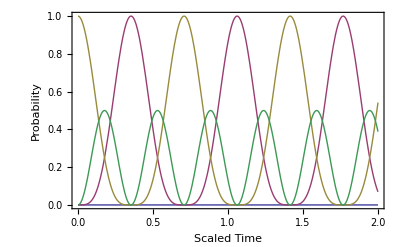

```mathematica
SuperFunction[HTC[1,1,1],{0,0,1,0},0,2][[1]]
```

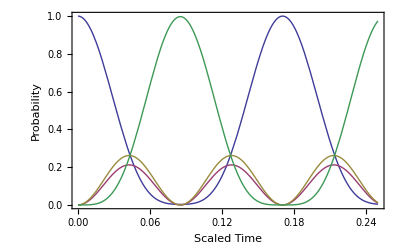

```mathematica
SuperFunction[HTC[10,.9,1],{1,0,0,0},0,.25][[1]]
```

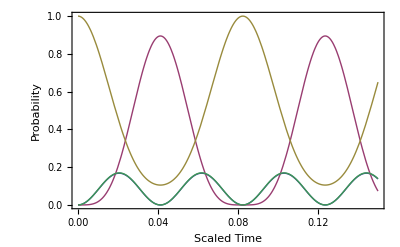

```mathematica
SuperFunction[HTC[100,.7,.5],{0,0,1,0},0,.15][[1]]
```

```mathematica
Manipulate[SuperFunction[HTC[2,N[Sin[x1]],N[Sin[x2]]],{1,0,0,0},0,1][[1]],{x1,0,2π,.1},{x2,0,2π,.1}]
```